This generates a KNF data set, returning concentrations of all species as functions of user-specified total oxygen and total hemoglobin concentrations given user-specified dissociation constants. Generates a user-specified number of data points between user-specified minimum and maximum partial pressures of oxygen.

```mathematica
KNFGenerateDataSetvH[
{kd1_, kd2_, kd3_, kd4_, totalHb_, minPO2_, maxPO2_, numPoints_}
] := Module[
{iterator,SOLUTIONSET, OUTPUT},
SOLUTIONSET = Table[
KNFSolvevH[
{kd1, kd2, kd3, kd4, iterator, totalHb}
],
{iterator, minPO2, maxPO2, (maxPO2 - minPO2) / (-1 + numPoints)}
];
OUTPUT = {};
Do[
OUTPUT = Append[
OUTPUT,
{
(* PO2 *)
minPO2 + (-1 + iterator) (maxPO2 - minPO2) / (-1 + numPoints),
(* YY *)
(* total sites occupied *)
(0 SOLUTIONSET[[iterator, 1, 2]] +  SOLUTIONSET[[iterator, 1, 3]] + 2 SOLUTIONSET[[iterator, 1, 4]] + 3 SOLUTIONSET[[iterator, 1, 5]] + 4 SOLUTIONSET[[iterator, 1, 6]]) 
/
(* total sites *)
(4(SOLUTIONSET[[iterator, 1, 2]] + SOLUTIONSET[[iterator, 1, 3]] + SOLUTIONSET[[iterator, 1, 4]] + SOLUTIONSET[[iterator, 1, 5]] + SOLUTIONSET[[iterator, 1, 6]])),
(* O2, T4RO20, T3RO21, T2RO22, T1RO23, T0RO24 *)
SOLUTIONSET[[iterator, 1, 1]],SOLUTIONSET[[iterator, 1, 2]],SOLUTIONSET[[iterator, 1, 3]], SOLUTIONSET[[iterator, 1, 4]], SOLUTIONSET[[iterator, 1, 5]], SOLUTIONSET[[iterator, 1, 6]]
}
],
{iterator, Length[SOLUTIONSET]}
];
OUTPUT
]

"Function KNFGenerateDataSetvH

Usage:

KNFGenerateDataSetvH[
{kd1_, kd2_, kd3_, kd4_, totalHb_, minPO2_, maxPO2_, numPoints_}
]

in which:
	kd1\t\tdissociation constant for the first oxygen binding event
	kd2\t\tdissociation constant for the second oxygen binding event
	kd3\t\tdissociation constant for the third oxygen binding event
	kd4\t\tdissociation constant for the fourth oxygen binding event
	totalHb\ttotal amount of hemoglobin in the system (molar)
	minPO2\t minimum partial pressure of oxygen above solution (torr)
	maxPO2\t maximum partial pressure of oxygen above solution (torr)
	numPoints  the number of points for which to compute solutions

Returns:

A list of length numPoints the elements of which are

{
PO2, Y, O2, T4RO20, T3RO21, T2RO22, T1RO23, T0RO24
}

in which:
	PO2\t   partial pressure of oxygen above solution (torr)
	Y\t\t fraction of available sites which are occupied by oxygen
	O2\t    concentration (molar) of oxygen in solution 
	T4RO20\tconcentration (molar) of the species to which no oxygen is bound
	T4RO21\tconcentration (molar) of the singly oxygen bound species
	T4RO22\tconcentration (molar) of the doubly oxygen bound species
	T4RO23\tconcentration (molar) of the triply oxygen bound species
	T4RO24\tconcentration (molar) of the quadruply oxygen bound species"
```

Function KNFGenerateDataSetvH

Usage:

KNFGenerateDataSetvH[
{kd1_, kd2_, kd3_, kd4_, totalHb_, minPO2_, maxPO2_, numPoints_}
]

in which:
	kd1		dissociation constant for the first oxygen binding event
	kd2		dissociation constant for the second oxygen binding event
	kd3		dissociation constant for the third oxygen binding event
	kd4		dissociation constant for the fourth oxygen binding event
	totalHb	total amount of hemoglobin in the system (molar)
	minPO2	 minimum partial pressure of oxygen above solution (torr)
	maxPO2	 maximum partial pressure of oxygen above solution (torr)
	numPoints  the number of points for which to compute solutions

Returns:

A list of length numPoints the elements of which are

{
PO2, Y, O2, T4RO20, T3RO21, T2RO22, T1RO23, T0RO24
}

in which:
	PO2	   partial pressure of oxygen above solution (torr)
	Y		 fraction of available sites which are occupied by oxygen
	O2	    concentration (molar) of oxygen in solution 
	T4RO20	concentration (molar) of the species to which no oxygen is bound
	T4RO21	concentration (molar) of the singly oxygen bound species
	T4RO22	concentration (molar) of the doubly oxygen bound species
	T4RO23	concentration (molar) of the triply oxygen bound species
	T4RO24	concentration (molar) of the quadruply oxygen bound species

Example:

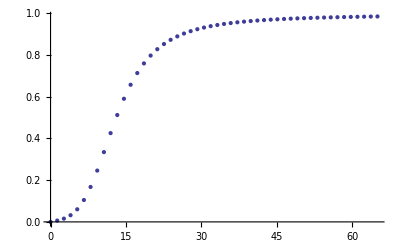

```mathematica
kd1 = .0001;
kd2 = .00005;
kd3 = .00001;
kd4 = .000005;

totalHb = .01;
minPO2 = .001;
maxPO2 = 65;
numPoints = 50;

arguments = {
kd1,kd2,kd3,kd4,totalHb, minPO2, maxPO2, numPoints
};

output = KNFGenerateDataSetvH[
arguments
];

ListPlot[
Transpose[
{#[[1]] & /@ output,
#[[2]] & /@ output}
]
]
```